```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["output.txt", "CSV"];
answer=614864614526014;
```

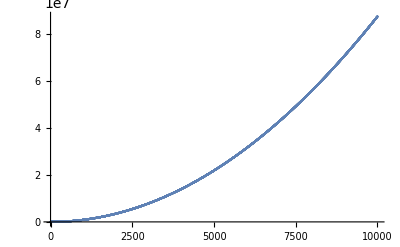

```mathematica
ListPlot[data]
```

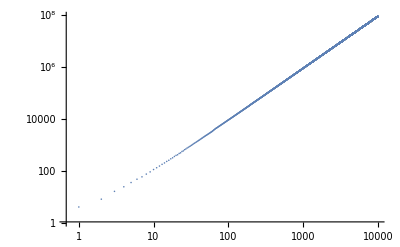

```mathematica
ListLogLogPlot[data]
```

```mathematica
slopes=Table[N[(Log[data[[index,2]]] - Log[data[[index-1,2]]])/(Log[data[[index,1]]] - Log[data[[index-1,1]]])],{index,2,Length[data]}];
```

```mathematica
Max[slopes]
```

3.13875

```mathematica
Mean[slopes]
```

1.99805

```mathematica
Median[slopes]
```

2.01328

```mathematica
StandardDeviation[slopes]
```

0.547155

This looks quadratic. So let’s try to fit the data.

```mathematica
fit=Fit[data[[100;;5000]],{x^2,x,1},x]
```

26.5324+1.60418 x+0.87548 x^2

Not liking those coefficients.

```mathematica
f[x_]:=26.5324427954966+1.6041826601319475 x+0.8754803995302209 x^2
```

```mathematica
data[[1001]]
f[1000]
```

{1000,877241}

877111.

```mathematica
data=Map[#[[2]]&,data];
```

```mathematica
group[data_,period_,i_]:=group[data,period,i]=Table[data[[j]],{j,i,Length[data],period}]
```

```mathematica
period = 1;
While[!Statistics`Library`ConstantVectorQ[Differences[group[data,period,1],2]],
period++;];
period
```

131

So a period of 131 ... the size of the maze

```mathematica
target=26501365;
remander = Mod[target,period]
d=Floor[target/period]
```

65

202300

202300 that is no accident

Time for the method of successive differences. Let’s get the first 2 differences

```mathematica
diff1=Differences[data];
```

```mathematica
diff2[i_]:=diff[i]=Differences[group[diff1,period,i]]
```

```mathematica
diff2[1]
```

{231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231,231}

Looks good. Now to check that all second differences are constant.

```mathematica
AllTrue[Table[Statistics`Library`ConstantVectorQ[diff2[i]], {i, 1, period}], #&]
```

True

Here are  the constants

```mathematica
constants=Table[diff2[i][[1]], {i, 1, period}]
```

{231,231,232,234,209,247,209,241,211,263,201,252,199,261,185,255,181,278,185,282,164,283,175,282,180,281,189,252,188,260,192,260,211,260,202,266,175,278,165,290,158,305,155,319,136,326,134,318,139,312,136,302,141,306,136,328,125,328,134,314,130,345,194,360,184,344,180,344,146,304,123,326,127,329,128,323,138,304,144,305,133,319,138,331,135,317,155,304,156,295,168,280,167,272,196,260,220,258,191,251,200,249,188,269,185,270,176,298,164,275,173,283,185,263,186,252,196,254,210,251,216,242,218,245,212,240,223,230,223,235,221}

```mathematica
solveDiff1[x_Integer]:=Module[{offset, start},
offset=Mod[x,period,1];
start=diff1[[offset]];
Return[start+constants[[offset]]*Floor[(x-offset)/period]];
]
```

```mathematica
AllTrue[Table[solveDiff1[i]==diff1[[i]],{i,1,Length[data]-1}],#&]
```

True

```mathematica
Table[solveDiff1[i],{i,1,20}]
```

{3,4,8,8,11,12,11,16,16,21,19,21,25,23,29,24,35,27,40,36}

```mathematica
diff1[[;;20]]
```

{3,4,8,8,11,12,11,16,16,21,19,21,25,23,29,24,35,27,40,36}

```mathematica
data[[;;20]]
```

{1,4,8,16,24,35,47,58,74,90,111,130,151,176,199,228,252,287,314,354}

```mathematica
solveDiff1[target]
```

37223292

```mathematica
solve[x_Integer]:=ParallelSum[solveDiff1[i],{i,1,x}]+1
```

```mathematica
Table[solve[x],{x,0,20}]
```

{1,4,8,16,24,35,47,58,74,90,111,130,151,176,199,228,252,287,314,354,390}

```mathematica
data[[;;21]]
```

{1,4,8,16,24,35,47,58,74,90,111,130,151,176,199,228,252,287,314,354,390}

```mathematica
AbsoluteTiming[solve[target]]
```

{13.1758,614864614526014}

```mathematica
%[[2]]==answer
```

True